#### Preamble

```mathematica
saveTask=CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]],15*60]; (*Saves nb each 15 minutes*)
StartScheduledTask[saveTask]
```

ScheduledTaskObject[…]

```mathematica
SetDirectory[NotebookDirectory[]]
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Nano_CSM_SDistAll.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Nano_CSM_Biosensor.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Optical_functions/Au_JohnsnChristy.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/GradientDescend.wls"
```

/home/juanathan/Documentos/Collaborations/2022-06-INAOE-CSM/3-Incrustamiento/FitDescensoGradiente

```mathematica
fs = 11;
texStyle={FontFamily->"Latin Modern Math",FontSize->fs,Black};
colors=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);

graphsOptsExp = {Mesh-> None,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 215, PlotStyle-> (Directive[Thick,#,Opacity[.5]]&/@colors)};
graphsOptsTeo = {Mesh-> None,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 215, PlotStyle-> (Directive[#]&/@colors)};
```

## Experimental data and theoretical with nominal values

### Code

#### Sample Characteristics

```mathematica
film = Import[#,"Data"]& @@ FileNames["1*fill.csv"];
TableForm[film[[2;;]],TableHeadings->{None,film[[1]]}]
radius = film[[2;;,2]];
muSigma = film[[2;;,{2,3}]];
cfrac = film[[2;;,4]]/100;
```

Nominal Au Thickness [+-0.2 nm] | Mean radius [nm] |  | Fill factor [100%] | 
3 | 5.78 | 1.89 | 20.3 | 0.6
5 | 7.3 | 2.3 | 22.1 | 0.1

```mathematica
nMat  = Import[#,"Data"] & @@ FileNames["3*Ind.csv"];
nMat = Drop[nMat,1];
nM = nMat[[1,2]]
```

1.33278

#### Experimental Spectra AuNI

```mathematica
(files = FileNames["*","Extinction*"])//TableForm
data = Import[#,"Data"]& /@ files;
wlen = Range[wlL = 450,wlR = 850,5.];
ang = {64.9,72.9} *Pi/180.;
nNP=JohnsonChristyAuRefSize[#1,#2]&;
pl = MapThread[Style["a = "<>ToString[#1]<>" nm, Θ = "<> ToString[#2],texStyle]&,{radius,cfrac}];
labels = Outer[#1<>" - θ_i = "<>#2<>"°"&,{"s-pol","p-pol"},ToString/@(ang*180/Pi)];
```

Extinction AuNI/Extinction AuNI nominal thickness d3nm_5nm 64_9deg.xlsx
Extinction AuNI/Extinction AuNI nominal thickness d3nm_5nm 72_9deg.xlsx

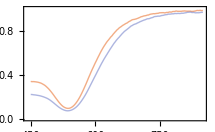
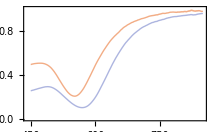
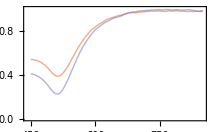
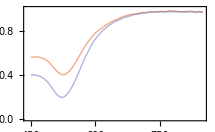

```mathematica
spectra = Map[Drop[#,4]&, data,{2}] (*Delete Headers*) ;
spectra = Map[Select[#,Function[list,wlL<=list[[1]]<= wlR]]&,spectra,{2}](*Choosing in the Visible*);
spectra = Map[Table[#[[{1,i}]]*{1,.01},{i,2,Length[#]}]&,spectra,{3}];
spectra = Transpose[spectra,{2,1,4,3,5}](*[[pol, ang, thickness, lda, Ext]]*);
spectra=spectra[[;;,;;,{1,2}]];

islandExt = Map[ListLinePlot[#,Evaluate[graphsOptsExp],PlotRange->{0,1}]&,spectra,{2}]
```

```mathematica
expResonances = Map[MinimalBy[#,Last]&, spectra,{3}] (*[[pol, ang, thickness]]*)
```

{{{{{536.713,0.0930782}},{{536.066,0.0709467}}},{{{552.366,0.204016}},{{569.534,0.0998457}}}},{{{{513.499,0.386172}},{{511.68,0.224258}}},{{{525.698,0.400039}},{{522.845,0.194133}}}}}

#### Poly

```mathematica
wlen = Range[wlL = 450,wlR = 850,5.];
ang = {64.9,72.9} *Pi/180.;
```

```mathematica
nominal = MapThread[ (
mu = First[#1];
sigma = Last[#1];
indAu = Transpose[Table[{nM,1.5},{i,wlen}]];
			norm2[CSMBioReflectionInt[ang,indAu,wlen,#2,{mu,sigma},"SizeDistribution"->"Normal"]])&,
{muSigma,cfrac}]; (*[[case, pol,ang,lda]]*)

nominal = Transpose[nominal,{3,1,2,4}](*[[pol,ang, case,lda]]*);
nominalplots = MapThread[ListLinePlot[#1,PlotLabel->#2,  DataRange->wlen[[{1,-1}]],Evaluate[graphsOptsTeo]]&,{nominal,labels},2];
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

### Results

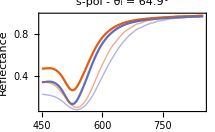
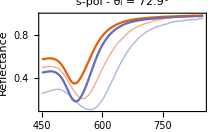
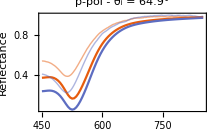
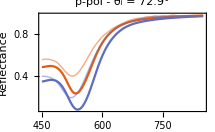

```mathematica
MapThread[Show[{#1,#2},PlotRange->All, FrameLabel-> (Style[#,texStyle]&/@{"Wavelength [nm]","Reflectance"})]&,{nominalplots,islandExt},2]
```

## Gradient Descend Method

## 450 nm a 850 nm

### p Pol - Matrix refractive index

#### Calculation

{2,2,2,3138,2}

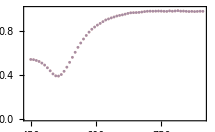
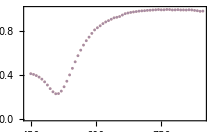
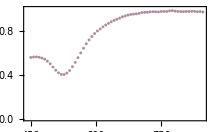
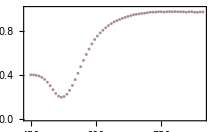

```mathematica
denXXX = 50; (*den050-> 50, den100->100, den25->25*)
pol = 2; (*p Pol*)

spectra//Dimensions (*[[pol, ang, thickness, lda, Ext]]*)
wl = spectra[[1,1,1,;;,1]];
take = Range[1,3138,denXXX];
lambda = wl[[take]];
Map[ListPlot[{#[[take,2]],#[[take,2]]},DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsExp]]&,spectra[[pol]],{2}]
```

```mathematica
bestFit = ParallelTable[
            {mu, sigma} = muSigma[[c]];
            f = norm2[CSMBioReflectionInt[ang[[t]],
                                          Transpose[Table[{#,1.5},{i,lambda}]], (*{nMat, nSus}*)
                                          lambda,
                                          cfrac[[c]],
                                          muSigma[[c]],
                                          "SizeDistribution"->"Normal"][[pol]]]&;
            y = spectra[[pol,t,c,take,2]];
            error = Plus @@ (f[#] - y)^2/Length[lambda]&;
            result = AbsoluteTiming[
                        Prepend[
                              NGradientDescent[error,{1.33},LearningRate -> "Barzilai-Borwein",Tolerance-> 1.*^-5],
                              {{"s Pol","p Pol"}[[pol]], ang[[t]]*180./Pi, mu}]  ];
             Print[{Date[], "\n", result}];
             result[[2]],
      {t, Length[ang]},
      {c,Length[muSigma]}];
```

{{2024,3,10,17,12,53.638522},
,{246.063,{{p Pol,72.9,5.78},{1.29658},9.26873×10^-7}}}

{{2024,3,10,17,16,32.797144},
,{219.158,{{p Pol,72.9,7.3},{1.2947},1.19354×10^-6}}}

{{2024,3,10,17,19,53.208173},
,{665.633,{{p Pol,64.9,5.78},{2.45546},40.2113}}}

{{2024,3,10,17,24,44.722588},
,{291.514,{{p Pol,64.9,7.3},{1.34455},0.793819}}}

```mathematica
num = Length[FileNames["*", dir = "1-Fits"]];
exportData = Prepend[Flatten[Array[Flatten[bestFit[[#1,#2]]] &,{2,2}],1],
                      {"Pol", "ang","mu","Best RefIndex","Error"}];
TableForm[exportData]
Export[FileNameJoin[{dir,"BestRefIndMat-pPol-450nm-850nm-dens050.csv"}],exportData];
```

Pol | ang | mu | Best RefIndex | Error
p Pol | 64.9 | 5.78 | 2.45546 | 40.2113
p Pol | 64.9 | 7.3 | 1.34455 | 0.793819
p Pol | 72.9 | 5.78 | 1.29658 | 9.26873×10^-7
p Pol | 72.9 | 7.3 | 1.2947 | 1.19354×10^-6

#### Results

```mathematica
parameters = Drop[Import[FileNameJoin[{dir,"BestRefIndMat-pPol-450nm-850nm-dens050.csv"}],"Data"],1];
parameters = Partition[#[[4]]&/@ parameters,2];
pol = 2;
take = Range[1,3138,25];
lambda = wl[[take]];
fitResultsGraph = {0,0,0};
```

```mathematica
fitResults = Array[(
                nMatFit = parameters[[#1,#2]];
                f = norm2[CSMBioReflectionInt[ang[[#1]],
                                          Transpose[Table[{nMatFit,1.5},{i,lambda}]], (*{nMat, nSus}*)
                                          lambda,
                                          cfrac[[#2]],
                                          muSigma[[#2]],
                                          "SizeDistribution"->"Normal"][[pol]]])&,
            Dimensions[parameters]];
resonances = Map[MinimalBy[Transpose[{lambda,#}],Last]&, fitResults,{2}] 
expRes = expResonances[[pol]]
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{{{599.259,0.000623231}},{{525.05,0.0511769}}},{{{531.532,0.342637}},{{534.77,0.17149}}}}

{{{{513.499,0.386172}},{{511.68,0.224258}}},{{{525.698,0.400039}},{{522.845,0.194133}}}}

```mathematica
fitResultsGraph[[1]] = ListPlot[Callout[#,NumberForm[#[[1,1]],{4,1}],Right,LabelStyle->texStyle], PlotStyle-> Directive[Magenta,PointSize[.025]] ] & /@ Flatten[resonances,1];
fitResultsGraph[[1]] = Partition[fitResultsGraph[[1]],2]
fitResultsGraph[[2]] = ListPlot[Callout[#,NumberForm[#[[1,1]],{4,1}],Right,LabelStyle->texStyle], PlotStyle-> Directive[Cyan,PointSize[.025]] ] & /@ Flatten[expRes,1];
fitResultsGraph[[2]] = Partition[fitResultsGraph[[2]],2]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

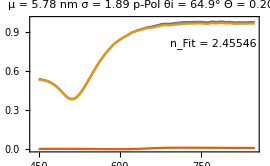
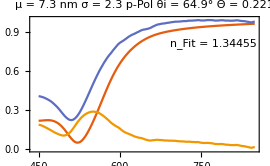
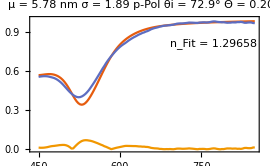
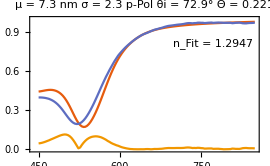

```mathematica
lb = Array[(sigma = "μ = "<>ToString@muSigma[[#2,1]]<>" nm σ = "<>ToString@muSigma[[#2,2]];
       polLab = {"s-Pol","p-Pol"}[[pol]];
       cf = "Θ = "<>ToString@cfrac[[#2]];
       deg = "θi = "<> ToString[ang[[#1]]/Degree]<>"°";
        sigma<>" "<>polLab<>" "<>deg<>" "<>cf)&,
{2,2}];

fitResultsGraph[[3]] = MapThread[
  ListLinePlot[{#1,#2[[take,2]],Abs[#1-#2[[take,2]]]},
                DataRange->lambda[[{1,-1}]],
                PlotRange->1,
                ImageSize->270,
                PlotLabel->Style[#3,texStyle],Evaluate[graphsOptsTeo],
    Epilog->{Inset[Style["n_Fit = "<> ToString[#4],texStyle],Scaled[{.8,.8}]]}]&,
    {fitResults, spectra[[2]], lb, parameters},2]
```

#### Results summary

```mathematica
Grid@MapThread[Show, Reverse@fitResultsGraph,2]
```

-Graphics-

### s Pol - Matrix refractive index

#### Calculation

{2,2,2,3138,2}

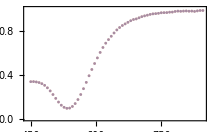
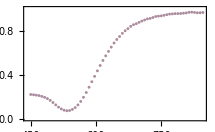
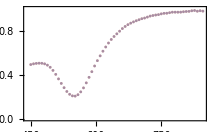
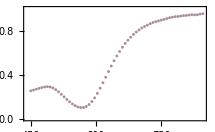

```mathematica
denXXX = 50; (*den050-> 50, den100->100, den25->25*)
pol = 1; (*p Pol*)

spectra//Dimensions (*[[pol, ang, thickness, lda, Ext]]*)
wl = spectra[[1,1,1,;;,1]];
take = Range[1,3138,denXXX];
lambda = wl[[take]];
Map[ListPlot[{#[[take,2]],#[[take,2]]},DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsExp]]&,spectra[[pol]],{2}]
```

```mathematica
bestFit = ParallelTable[
            {mu, sigma} = muSigma[[c]];
            f = norm2[CSMBioReflectionInt[ang[[t]],
                                          Transpose[Table[{#,1.5},{i,lambda}]], (*{nMat, nSus}*)
                                          lambda,
                                          cfrac[[c]],
                                          muSigma[[c]],
                                          "SizeDistribution"->"Normal"][[pol]]]&;
            y = spectra[[pol,t,c,take,2]];
            error = Plus @@ (f[#] - y)^2/Length[lambda]&;
            result = AbsoluteTiming[
                        Prepend[
                              NGradientDescent[error,{1.33},LearningRate -> "Barzilai-Borwein",Tolerance-> 1.*^-5],
                              {{"s Pol","p Pol"}[[pol]], ang[[t]]*180./Pi, mu}]  ];
             Print[{Date[], "\n", result}];
             result[[2]],
      {t, Length[ang]},
      {c,Length[muSigma]}];
```

{{2024,3,10,18,8,59.926203},
,{440.672,{{s Pol,72.9,5.78},{1.3895},2.72144×10^-6}}}

{{2024,3,10,18,14,27.460324},
,{327.534,{{s Pol,72.9,7.3},{1.49101},13.0539}}}

{{2024,3,10,18,51,4.256478},
,{2965.,{{s Pol,64.9,5.78},{1.34964},0.511107}}}

{{2024,3,10,18,56,32.369031},
,{328.112,{{s Pol,64.9,7.3},{1.34072},0.688236}}}

```mathematica
num = Length[FileNames["*", dir = "1-Fits"]];
exportData = Prepend[Flatten[Array[Flatten[bestFit[[#1,#2]]] &,{2,2}],1],
                      {"Pol", "ang","mu","Best RefIndex","Error"}];
TableForm[exportData]
Export[FileNameJoin[{dir,"BestRefIndMat-sPol-450nm-850nm-dens050.csv"}],exportData];
```

Pol | ang | mu | Best RefIndex | Error
s Pol | 64.9 | 5.78 | 1.34964 | 0.511107
s Pol | 64.9 | 7.3 | 1.34072 | 0.688236
s Pol | 72.9 | 5.78 | 1.3895 | 2.72144×10^-6
s Pol | 72.9 | 7.3 | 1.49101 | 13.0539

#### Results

```mathematica
parameters = Drop[Import[FileNameJoin[{dir,"BestRefIndMat-sPol-450nm-850nm-dens050.csv"}],"Data"],1];
parameters = Partition[#[[4]]&/@ parameters,2];
pol = 1;
take = Range[1,3138,25];
lambda = wl[[take]];
fitResultsGraph = {0,0,0};
```

```mathematica
fitResults = Array[(
                nMatFit = parameters[[#1,#2]];
                f = norm2[CSMBioReflectionInt[ang[[#1]],
                                          Transpose[Table[{nMatFit,1.5},{i,lambda}]], (*{nMat, nSus}*)
                                          lambda,
                                          cfrac[[#2]],
                                          muSigma[[#2]],
                                          "SizeDistribution"->"Normal"][[pol]]])&,
            Dimensions[parameters]];
resonances = Map[MinimalBy[Transpose[{lambda,#}],Last]&, fitResults,{2}] 
expRes = expResonances[[pol]]
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{{{525.05,0.218646}},{{525.05,0.110282}}},{{{534.77,0.124821}},{{848.408,0.0425413}}}}

{{{{536.713,0.0930782}},{{536.066,0.0709467}}},{{{552.366,0.204016}},{{569.534,0.0998457}}}}

```mathematica
fitResultsGraph[[1]] = ListPlot[Callout[#,NumberForm[#[[1,1]],{4,1}],Right,LabelStyle->texStyle], PlotStyle-> Directive[Magenta,PointSize[.025]] ] & /@ Flatten[resonances,1];
fitResultsGraph[[1]] = Partition[fitResultsGraph[[1]],2]
fitResultsGraph[[2]] = ListPlot[Callout[#,NumberForm[#[[1,1]],{4,1}],Right,LabelStyle->texStyle], PlotStyle-> Directive[Cyan,PointSize[.025]] ] & /@ Flatten[expRes,1];
fitResultsGraph[[2]] = Partition[fitResultsGraph[[2]],2]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

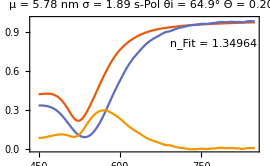
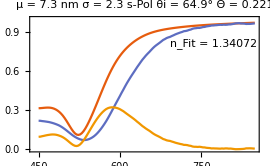
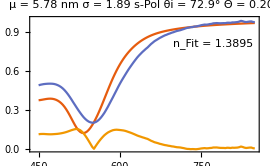
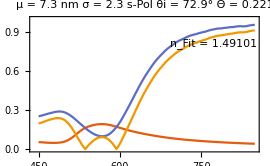

```mathematica
lb = Array[(sigma = "μ = "<>ToString@muSigma[[#2,1]]<>" nm σ = "<>ToString@muSigma[[#2,2]];
       polLab = {"s-Pol","p-Pol"}[[pol]];
       cf = "Θ = "<>ToString@cfrac[[#2]];
       deg = "θi = "<> ToString[ang[[#1]]/Degree]<>"°";
        sigma<>" "<>polLab<>" "<>deg<>" "<>cf)&,
{2,2}];

fitResultsGraph[[3]] = MapThread[
  ListLinePlot[{#1,#2[[take,2]],Abs[#1-#2[[take,2]]]},
                DataRange->lambda[[{1,-1}]],
                PlotRange->1,
                ImageSize->270,
                PlotLabel->Style[#3,texStyle],Evaluate[graphsOptsTeo],
    Epilog->{Inset[Style["n_Fit = "<> ToString[#4],texStyle],Scaled[{.8,.8}]]}]&,
    {fitResults, spectra[[pol]], lb, parameters},2]
```

#### Results summary

```mathematica
Grid@MapThread[Show, Reverse@fitResultsGraph,2]
```

-Graphics-

### p Pol - Matrix refractive index - radius

#### Calculation

{2,2,2,3138,2}

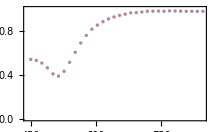
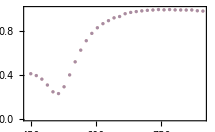
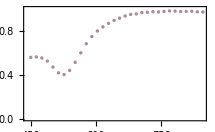
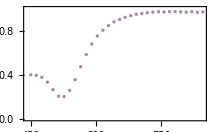

```mathematica
denXXX = 100; (*den050-> 50, den100->100, den25->25*)
pol = 2; (*p Pol*)

spectra//Dimensions (*[[pol, ang, thickness, lda, Ext]]*)
wl = spectra[[1,1,1,;;,1]];
take = Range[1,3138,denXXX];
lambda = wl[[take]];
Map[ListPlot[{#[[take,2]],#[[take,2]]},DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsExp]]&,spectra[[pol]],{2}]
```

```mathematica
pol = 2; (*p Pol*)

bestFit = ParallelTable[
            {mu, sigma} = muSigma[[c]];
            f = norm2[CSMBioReflectionInt[ang[[t]],
                                          Transpose[Table[{#1,1.5},{i,lambda}]], (*{nMat, nSus}*)
                                          lambda,
                                          cfrac[[c]],
                                          {#2,sigma},
                                          "SizeDistribution"->"Normal"][[pol]]]&;
            y = spectra[[pol,t,c,take,2]];
            error = Plus @@ (f[#1,#2] - y)^2/Length[lambda]&;
            result = AbsoluteTiming[
                        Prepend[
                              NGradientDescent[error,{1.33,3.5},LearningRate -> "Barzilai-Borwein",Tolerance-> 1.*^-5],
                              {{"s Pol","p Pol"}[[pol]], ang[[t]]*180./Pi, mu}]  ];
             Print[{Date[], "\n", result}];
             result[[2]],
      {t, Length[ang]},
      {c,Length[muSigma]}];
```

{{2024,3,10,21,41,17.734541},
,{248.301,{{p Pol,72.9,5.78},{1.31941,3.50997},5.30348×10^-7}}}

{{2024,3,10,21,45,36.927928},
,{259.193,{{p Pol,72.9,7.3},{1.3188,3.51018},7.00619×10^-7}}}

{{2024,3,10,21,55,17.37275},
,{1087.94,{{p Pol,64.9,5.78},{1.79009,3.32676},19.776}}}

{{2024,3,10,23,22,39.729161},
,{5242.36,{{p Pol,64.9,7.3},{0.000328354,4.20415},1.79165}}}

```mathematica
exportData = Prepend[Flatten[Array[Flatten[bestFit[[#1,#2]]] &,{2,2}],1],
                      {"Pol", "ang","mu","Best RefIndex","Best radius","Error"}]
```

{{Pol,ang,mu,Best RefIndex,Best radius,Error},{p Pol,64.9,5.78,1.79009,3.32676,19.776},{p Pol,64.9,7.3,0.000328354,4.20415,1.79165},{p Pol,72.9,5.78,1.31941,3.50997,5.30348×10^-7},{p Pol,72.9,7.3,1.3188,3.51018,7.00619×10^-7}}

```mathematica
num = Length[FileNames["*", dir = "1-Fits"]];
exportData = Prepend[Flatten[Array[Flatten[bestFit[[#1,#2]]] &,{2,2}],1],
                      {"Pol", "ang","mu","BestRefIndex","BestRadius","Error"}];
TableForm[exportData]
Export[FileNameJoin[{dir,"BestRefIndMat-rad-pPol-450nm-850nm-dens100.csv"}],exportData];
```

Pol | ang | mu | BestRefIndex | Bestradius | Error
p Pol | 64.9 | 5.78 | 1.79009 | 3.32676 | 19.776
p Pol | 64.9 | 7.3 | 0.000328354 | 4.20415 | 1.79165
p Pol | 72.9 | 5.78 | 1.31941 | 3.50997 | 5.30348×10^-7
p Pol | 72.9 | 7.3 | 1.3188 | 3.51018 | 7.00619×10^-7

#### Results

```mathematica
parameters = Drop[Import[FileNameJoin[{dir,"BestRefIndMat-rad-pPol-450nm-850nm-dens100.csv"}],"Data"],1]
parameters = Partition[#[[{4,5}]]&/@ parameters,2]
pol = 2;
take = Range[1,3138,25];
lambda = wl[[take]];
fitResultsGraph = {0,0,0};
```

{{p Pol,64.9,5.78,1.79009,3.32676,19.776},{p Pol,64.9,7.3,0.000328354,4.20415,1.79165},{p Pol,72.9,5.78,1.31941,3.50997,5.30348×10^-7},{p Pol,72.9,7.3,1.3188,3.51018,7.00619×10^-7}}

{{{1.79009,3.32676},{0.000328354,4.20415}},{{1.31941,3.50997},{1.3188,3.51018}}}

```mathematica
fitResults = Array[(
                nMatFit = parameters[[#1,#2,1]];
                radFit = parameters[[#1,#2,2]];
                f = norm2[CSMBioReflectionInt[ang[[#1]],
                                          Transpose[Table[{nMatFit,1.5},{i,lambda}]], (*{nMat, nSus}*)
                                          lambda,
                                          cfrac[[#2]],
                                          {radFit, muSigma[[#2,2]]},
                                          "SizeDistribution"->"Normal"][[pol]]])&,
            (*Dimensions[parameters]*){2,2}];
resonances = Map[MinimalBy[Transpose[{lambda,#}],Last]&, fitResults,{2}] 
expRes = expResonances[[pol]]
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{{{848.408,0.0160478}},{{476.264,1.},{486.045,1.},{515.317,1.},{518.563,1.}}},{{{531.532,0.376788}},{{534.77,0.216073}}}}

{{{{513.499,0.386172}},{{511.68,0.224258}}},{{{525.698,0.400039}},{{522.845,0.194133}}}}

```mathematica
fitResultsGraph[[1]] = ListPlot[Callout[#,NumberForm[#[[1,1]],{4,1}],Right,LabelStyle->texStyle], PlotStyle-> Directive[Magenta,PointSize[.025]] ] & /@ Flatten[resonances,1];
fitResultsGraph[[1]] = Partition[fitResultsGraph[[1]],2]
fitResultsGraph[[2]] = ListPlot[Callout[#,NumberForm[#[[1,1]],{4,1}],Right,LabelStyle->texStyle], PlotStyle-> Directive[Cyan,PointSize[.025]] ] & /@ Flatten[expRes,1];
fitResultsGraph[[2]] = Partition[fitResultsGraph[[2]],2]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

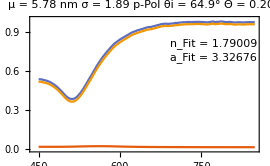
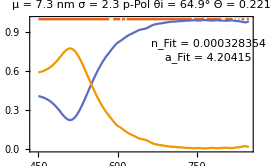
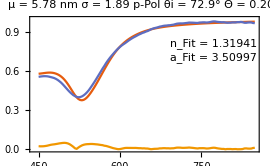
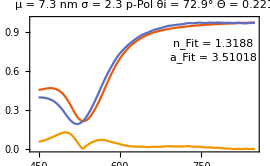

```mathematica
lb = Array[(sigma = "μ = "<>ToString@muSigma[[#2,1]]<>" nm σ = "<>ToString@muSigma[[#2,2]];
       polLab = {"s-Pol","p-Pol"}[[pol]];
       cf = "Θ = "<>ToString@cfrac[[#2]];
       deg = "θi = "<> ToString[ang[[#1]]/Degree]<>"°";
        sigma<>" "<>polLab<>" "<>deg<>" "<>cf)&,
{2,2}];

fitResultsGraph[[3]] = MapThread[
  ListLinePlot[{#1,#2[[take,2]],Abs[#1-#2[[take,2]]]},
                DataRange->lambda[[{1,-1}]],
                PlotRange->1,
                ImageSize->270,
                PlotLabel->Style[#3,texStyle],Evaluate[graphsOptsTeo],
    Epilog->{Inset[Style["n_Fit = "<> ToString[#4[[1]]],texStyle],Scaled[{.8,.8}]],
            Inset[Style["a_Fit = "<> ToString[#4[[2]]],texStyle],Scaled[{.8,.7}]]}]&,
    {fitResults, spectra[[2]], lb, parameters},2]
```

#### Results summary

```mathematica
Grid@MapThread[Show, Reverse@fitResultsGraph,2]
```

-Graphics-

### s Pol - Matrix refractive index - radius

#### Calculation

{2,2,2,3138,2}

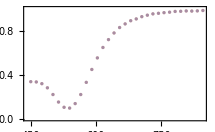
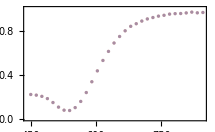
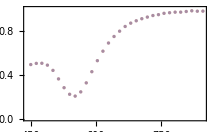
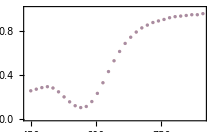

```mathematica
denXXX = 100; (*den050-> 50, den100->100, den25->25*)
pol = 1; (*p Pol*)

spectra//Dimensions (*[[pol, ang, thickness, lda, Ext]]*)
wl = spectra[[1,1,1,;;,1]];
take = Range[1,3138,denXXX];
lambda = wl[[take]];
Map[ListPlot[{#[[take,2]],#[[take,2]]},DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsExp]]&,spectra[[pol]],{2}]
```

```mathematica
bestFit = ParallelTable[
            {mu, sigma} = muSigma[[c]];
            f = norm2[CSMBioReflectionInt[ang[[t]],
                                          Transpose[Table[{Abs[#1],1.5},{i,lambda}]], (*{nMat, nSus}*)
                                          lambda,
                                          cfrac[[c]],
                                          {Abs[#2],sigma},
                                          "SizeDistribution"->"Normal"][[pol]]]&;
            y = spectra[[pol,t,c,take,2]];
            error = Plus @@ (f[#1,#2] - y)^2/Length[lambda]&;
            result = AbsoluteTiming[
                        Prepend[
                              NGradientDescent[error,{1.33,3.5},LearningRate -> "Barzilai-Borwein",Tolerance-> 1.*^-5],
                              {{"s Pol","p Pol"}[[pol]], ang[[t]]*180./Pi, mu}]  ];
             Print[{Date[], "\n", result}];
             result[[2]],
      {t, Length[ang]},
      {c,Length[muSigma]}];
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{2024,3,11,0,46,41.705575},
,{1318.82,{{s Pol,72.9,5.78},{-0.000100295,2.23825},3.15088}}}

{{2024,3,11,0,54,36.368935},
,{474.663,{{s Pol,72.9,7.3},{2.4881,3.50152},2.5278×10^-8}}}

{{2024,3,11,7,12,13.08722},
,{24450.2,{{s Pol,64.9,5.78},{1.35228,3.51094},0.391334}}}

{{2024,3,11,7,31,42.91055},
,{1169.79,{{s Pol,64.9,7.3},{1.34691,3.50845},0.484119}}}

```mathematica
num = Length[FileNames["*", dir = "1-Fits"]];
exportData = Prepend[Flatten[Array[Flatten[bestFit[[#1,#2]]] &,{2,2}],1],
                      {"Pol", "ang","mu","BestRefIndex","BestRadius","Error"}];
TableForm[exportData]
Export[FileNameJoin[{dir,"BestRefIndMat-rad-sPol-450nm-850nm-dens100.csv"}],exportData];
```

Pol | ang | mu | BestRefIndex | BestRadius | Error
s Pol | 64.9 | 5.78 | 1.35228 | 3.51094 | 0.391334
s Pol | 64.9 | 7.3 | 1.34691 | 3.50845 | 0.484119
s Pol | 72.9 | 5.78 | -0.000100295 | 2.23825 | 3.15088
s Pol | 72.9 | 7.3 | 2.4881 | 3.50152 | 2.5278×10^-8

#### Results

```mathematica
parameters = Drop[Import[FileNameJoin[{dir,"BestRefIndMat-rad-sPol-450nm-850nm-dens100.csv"}],"Data"],1]
parameters = Partition[#[[{4,5}]]&/@ parameters,2]
pol = 1;
take = Range[1,3138,25];
lambda = wl[[take]];
fitResultsGraph = {0,0,0};
```

{{s Pol,64.9,5.78,1.35228,3.51094,0.391334},{s Pol,64.9,7.3,1.34691,3.50845,0.484119},{s Pol,72.9,5.78,-0.000100295,2.23825,3.15088},{s Pol,72.9,7.3,2.4881,3.50152,2.5278×10^-8}}

{{{1.35228,3.51094},{1.34691,3.50845}},{{-0.000100295,2.23825},{2.4881,3.50152}}}

```mathematica
fitResults = Array[(
                nMatFit = Abs@parameters[[#1,#2,1]];
                radFit = parameters[[#1,#2,2]];
                f = norm2[CSMBioReflectionInt[ang[[#1]],
                                          Transpose[Table[{nMatFit,1.5},{i,lambda}]], (*{nMat, nSus}*)
                                          lambda,
                                          cfrac[[#2]],
                                          {radFit, muSigma[[#2,2]]},
                                          "SizeDistribution"->"Normal"][[pol]]])&,
            (*Dimensions[parameters]*){2,2}];
resonances = Map[MinimalBy[Transpose[{lambda,#}],Last]&, fitResults,{2}] 
expRes = expResonances[[pol]]
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{{{525.05,0.300809}},{{525.05,0.189063}}},{{{450.121,0.9998}},{{848.408,0.456189}}}}

{{{{536.713,0.0930782}},{{536.066,0.0709467}}},{{{552.366,0.204016}},{{569.534,0.0998457}}}}

```mathematica
expResonances
```

{{{{{536.713,0.0930782}},{{536.066,0.0709467}}},{{{552.366,0.204016}},{{569.534,0.0998457}}}},{{{{513.499,0.386172}},{{511.68,0.224258}}},{{{525.698,0.400039}},{{522.845,0.194133}}}}}

```mathematica
fitResultsGraph[[1]] = ListPlot[Callout[#,NumberForm[#[[1,1]],{4,1}],Right,LabelStyle->texStyle], PlotStyle-> Directive[Magenta,PointSize[.025]] ] & /@ Flatten[resonances,1];
fitResultsGraph[[1]] = Partition[fitResultsGraph[[1]],2]
fitResultsGraph[[2]] = ListPlot[Callout[#,NumberForm[#[[1,1]],{4,1}],Right,LabelStyle->texStyle], PlotStyle-> Directive[Cyan,PointSize[.025]] ] & /@ Flatten[expRes,1];
fitResultsGraph[[2]] = Partition[fitResultsGraph[[2]],2]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

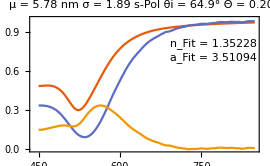
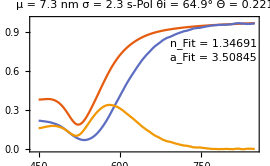
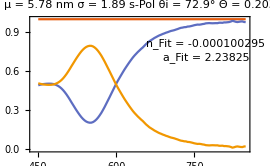
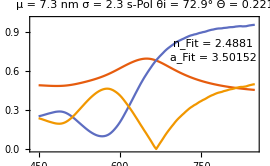

```mathematica
lb = Array[(sigma = "μ = "<>ToString@muSigma[[#2,1]]<>" nm σ = "<>ToString@muSigma[[#2,2]];
       polLab = {"s-Pol","p-Pol"}[[pol]];
       cf = "Θ = "<>ToString@cfrac[[#2]];
       deg = "θi = "<> ToString[ang[[#1]]/Degree]<>"°";
        sigma<>" "<>polLab<>" "<>deg<>" "<>cf)&,
{2,2}];

fitResultsGraph[[3]] = MapThread[
  ListLinePlot[{#1,#2[[take,2]],Abs[#1-#2[[take,2]]]},
                DataRange->lambda[[{1,-1}]],
                PlotRange->1,
                ImageSize->270,
                PlotLabel->Style[#3,texStyle],Evaluate[graphsOptsTeo],
    Epilog->{Inset[Style["n_Fit = "<> ToString[#4[[1]]],texStyle],Scaled[{.8,.8}]],
            Inset[Style["a_Fit = "<> ToString[#4[[2]]],texStyle],Scaled[{.8,.7}]]}]&,
    {fitResults, spectra[[pol]], lb, parameters},2]
```

#### Results summary

```mathematica
Grid@MapThread[Show, Reverse@fitResultsGraph,2]
```

-Graphics-

## 450 nm a 700 nm

### p Pol - Matrix refractive index

#### Calculation

{2,2,2,3138,2}

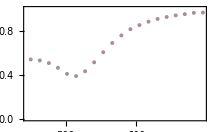
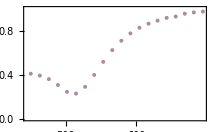
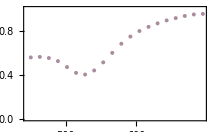
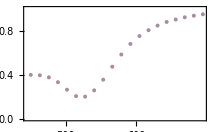

```mathematica
denXXX = 100; (*den050-> 50, den100->100, den25->25*)
pol = 2; (*p Pol*)

spectra//Dimensions (*[[pol, ang, thickness, lda, Ext]]*)
wl = spectra[[1,1,1,;;,1]];
take = Range[1,2000,denXXX];
lambda = wl[[take]];
Map[ListPlot[{#[[take,2]],#[[take,2]]},DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsExp]]&,spectra[[pol]],{2}]
```

```mathematica
bestFit = ParallelTable[
            {mu, sigma} = muSigma[[c]];
            f = norm2[CSMBioReflectionInt[ang[[t]],
                                          Transpose[Table[{#,1.5},{i,lambda}]], (*{nMat, nSus}*)
                                          lambda,
                                          cfrac[[c]],
                                          muSigma[[c]],
                                          "SizeDistribution"->"Normal"][[pol]]]&;
            y = spectra[[pol,t,c,take,2]];
            error = Plus @@ (f[#] - y)^2/Length[lambda]&;
            result = AbsoluteTiming[
                        Prepend[
                              NGradientDescent[error,{1.33},LearningRate -> "Barzilai-Borwein",Tolerance-> 1.*^-5],
                              {{"s Pol","p Pol"}[[pol]], ang[[t]]*180./Pi, mu}]  ];
             Print[{Date[], "\n", result}];
             result[[2]],
      {t, Length[ang]},
      {c,Length[muSigma]}];
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{2024,3,10,21,24,29.83411},
,{90.0027,{{p Pol,72.9,5.78},{1.29648},6.60756×10^-7}}}

{{2024,3,10,21,25,52.161241},
,{82.327,{{p Pol,72.9,7.3},{1.29589},8.3789×10^-7}}}

{{2024,3,10,21,26,30.886101},
,{211.055,{{p Pol,64.9,5.78},{1.70943},9.23536}}}

{{2024,3,10,21,28,6.073071},
,{95.1868,{{p Pol,64.9,7.3},{1.34392},0.4762}}}

```mathematica
num = Length[FileNames["*", dir = "1-Fits"]];
exportData = Prepend[Flatten[Array[Flatten[bestFit[[#1,#2]]] &,{2,2}],1],
                      {"Pol", "ang","mu","Best RefIndex","Error"}];
TableForm[exportData]
Export[FileNameJoin[{dir,"BestRefIndMat-pPol-450nm-700nm-dens100.csv"}],exportData];
```

Pol | ang | mu | Best RefIndex | Error
p Pol | 64.9 | 5.78 | 1.70943 | 9.23536
p Pol | 64.9 | 7.3 | 1.34392 | 0.4762
p Pol | 72.9 | 5.78 | 1.29648 | 6.60756×10^-7
p Pol | 72.9 | 7.3 | 1.29589 | 8.3789×10^-7

#### Results

```mathematica
parameters = Drop[Import[FileNameJoin[{dir,"BestRefIndMat-pPol-450nm-700nm-dens100.csv"}],"Data"],1];
parameters = Partition[#[[4]]&/@ parameters,2];
pol = 2;
take = Range[1,3138,25];
lambda = wl[[take]];
fitResultsGraph = {0,0,0};
```

```mathematica
fitResults = Array[(
                nMatFit = parameters[[#1,#2]];
                f = norm2[CSMBioReflectionInt[ang[[#1]],
                                          Transpose[Table[{nMatFit,1.5},{i,lambda}]], (*{nMat, nSus}*)
                                          lambda,
                                          cfrac[[#2]],
                                          muSigma[[#2]],
                                          "SizeDistribution"->"Normal"][[pol]]])&,
            Dimensions[parameters]];
resonances = Map[MinimalBy[Transpose[{lambda,#}],Last]&, fitResults,{2}] 
expRes = expResonances[[pol]]
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{{{848.408,0.0136292}},{{525.05,0.0511067}}},{{{531.532,0.342952}},{{534.77,0.168392}}}}

{{{{513.499,0.386172}},{{511.68,0.224258}}},{{{525.698,0.400039}},{{522.845,0.194133}}}}

```mathematica
fitResultsGraph[[1]] = ListPlot[Callout[#,NumberForm[#[[1,1]],{4,1}],Right,LabelStyle->texStyle], PlotStyle-> Directive[Magenta,PointSize[.025]] ] & /@ Flatten[resonances,1];
fitResultsGraph[[1]] = Partition[fitResultsGraph[[1]],2]
fitResultsGraph[[2]] = ListPlot[Callout[#,NumberForm[#[[1,1]],{4,1}],Right,LabelStyle->texStyle], PlotStyle-> Directive[Cyan,PointSize[.025]] ] & /@ Flatten[expRes,1];
fitResultsGraph[[2]] = Partition[fitResultsGraph[[2]],2]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

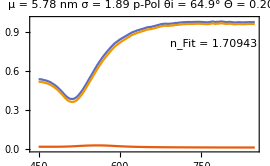
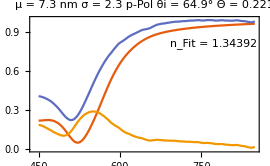
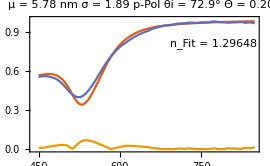
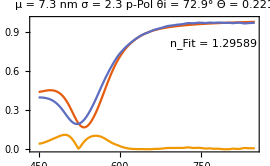

```mathematica
lb = Array[(sigma = "μ = "<>ToString@muSigma[[#2,1]]<>" nm σ = "<>ToString@muSigma[[#2,2]];
       polLab = {"s-Pol","p-Pol"}[[pol]];
       cf = "Θ = "<>ToString@cfrac[[#2]];
       deg = "θi = "<> ToString[ang[[#1]]/Degree]<>"°";
        sigma<>" "<>polLab<>" "<>deg<>" "<>cf)&,
{2,2}];

fitResultsGraph[[3]] = MapThread[
  ListLinePlot[{#1,#2[[take,2]],Abs[#1-#2[[take,2]]]},
                DataRange->lambda[[{1,-1}]],
                PlotRange->1,
                ImageSize->270,
                PlotLabel->Style[#3,texStyle],Evaluate[graphsOptsTeo],
    Epilog->{Inset[Style["n_Fit = "<> ToString[#4],texStyle],Scaled[{.8,.8}]]}]&,
    {fitResults, spectra[[2]], lb, parameters},2]
```

#### Results summary

```mathematica
Grid@MapThread[Show, Reverse@fitResultsGraph,2]
```

-Graphics-

### s Pol - Matrix refractive index

#### Calculation

{2,2,2,3138,2}

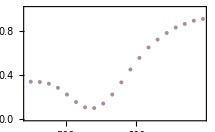
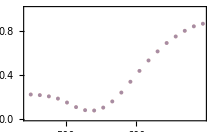
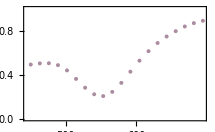
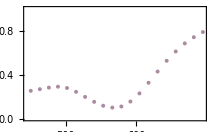

```mathematica
denXXX = 100; (*den050-> 50, den100->100, den25->25*)
pol = 1; (*p Pol*)

spectra//Dimensions (*[[pol, ang, thickness, lda, Ext]]*)
wl = spectra[[1,1,1,;;,1]];
take = Range[1,2000,denXXX];
lambda = wl[[take]];
Map[ListPlot[{#[[take,2]],#[[take,2]]},DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsExp]]&,spectra[[pol]],{2}]
```

```mathematica
bestFit = ParallelTable[
            {mu, sigma} = muSigma[[c]];
            f = norm2[CSMBioReflectionInt[ang[[t]],
                                          Transpose[Table[{#,1.5},{i,lambda}]], (*{nMat, nSus}*)
                                          lambda,
                                          cfrac[[c]],
                                          muSigma[[c]],
                                          "SizeDistribution"->"Normal"][[pol]]]&;
            y = spectra[[pol,t,c,take,2]];
            error = Plus @@ (f[#] - y)^2/Length[lambda]&;
            result = AbsoluteTiming[
                        Prepend[
                              NGradientDescent[error,{1.33},LearningRate -> "Barzilai-Borwein",Tolerance-> 1.*^-5],
                              {{"s Pol","p Pol"}[[pol]], ang[[t]]*180./Pi, mu}]  ];
             Print[{Date[], "\n", result}];
             result[[2]],
      {t, Length[ang]},
      {c,Length[muSigma]}];
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{2024,3,10,21,30,54.403368},
,{135.957,{{s Pol,72.9,5.78},{1.39015},1.80132×10^-6}}}

{{2024,3,10,21,33,3.36143},
,{128.958,{{s Pol,72.9,7.3},{1.47902},0.990349}}}

{{2024,3,10,21,33,29.614763},
,{291.168,{{s Pol,64.9,5.78},{1.35419},0.401444}}}

{{2024,3,10,21,36,23.893437},
,{174.279,{{s Pol,64.9,7.3},{1.35038},0.451094}}}

```mathematica
num = Length[FileNames["*", dir = "1-Fits"]];
exportData = Prepend[Flatten[Array[Flatten[bestFit[[#1,#2]]] &,{2,2}],1],
                      {"Pol", "ang","mu","Best RefIndex","Error"}];
TableForm[exportData]
Export[FileNameJoin[{dir,"BestRefIndMat-sPol-450nm-700nm-dens100.csv"}],exportData];
```

Pol | ang | mu | Best RefIndex | Error
s Pol | 64.9 | 5.78 | 1.35419 | 0.401444
s Pol | 64.9 | 7.3 | 1.35038 | 0.451094
s Pol | 72.9 | 5.78 | 1.39015 | 1.80132×10^-6
s Pol | 72.9 | 7.3 | 1.47902 | 0.990349

#### Results

```mathematica
parameters = Drop[Import[FileNameJoin[{dir,"BestRefIndMat-sPol-450nm-700nm-dens100.csv"}],"Data"],1];
parameters = Partition[#[[4]]&/@ parameters,2];
pol = 1;
take = Range[1,3138,25];
lambda = wl[[take]];
fitResultsGraph = {0,0,0};
```

```mathematica
fitResults = Array[(
                nMatFit = parameters[[#1,#2]];
                f = norm2[CSMBioReflectionInt[ang[[#1]],
                                          Transpose[Table[{nMatFit,1.5},{i,lambda}]], (*{nMat, nSus}*)
                                          lambda,
                                          cfrac[[#2]],
                                          muSigma[[#2]],
                                          "SizeDistribution"->"Normal"][[pol]]])&,
            Dimensions[parameters]];
resonances = Map[MinimalBy[Transpose[{lambda,#}],Last]&, fitResults,{2}] 
expRes = expResonances[[pol]]
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{{{525.05,0.213766}},{{521.807,0.101301}}},{{{534.77,0.122558}},{{479.525,0.0373496}}}}

{{{{536.713,0.0930782}},{{536.066,0.0709467}}},{{{552.366,0.204016}},{{569.534,0.0998457}}}}

```mathematica
fitResultsGraph[[1]] = ListPlot[Callout[#,NumberForm[#[[1,1]],{4,1}],Right,LabelStyle->texStyle], PlotStyle-> Directive[Magenta,PointSize[.025]] ] & /@ Flatten[resonances,1];
fitResultsGraph[[1]] = Partition[fitResultsGraph[[1]],2]
fitResultsGraph[[2]] = ListPlot[Callout[#,NumberForm[#[[1,1]],{4,1}],Right,LabelStyle->texStyle], PlotStyle-> Directive[Cyan,PointSize[.025]] ] & /@ Flatten[expRes,1];
fitResultsGraph[[2]] = Partition[fitResultsGraph[[2]],2]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

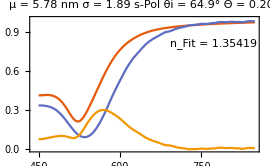
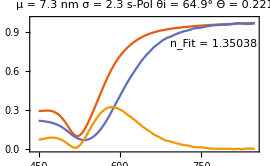
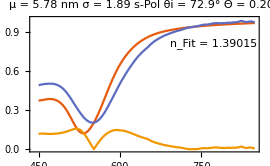
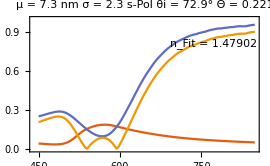

```mathematica
lb = Array[(sigma = "μ = "<>ToString@muSigma[[#2,1]]<>" nm σ = "<>ToString@muSigma[[#2,2]];
       polLab = {"s-Pol","p-Pol"}[[pol]];
       cf = "Θ = "<>ToString@cfrac[[#2]];
       deg = "θi = "<> ToString[ang[[#1]]/Degree]<>"°";
        sigma<>" "<>polLab<>" "<>deg<>" "<>cf)&,
{2,2}];

fitResultsGraph[[3]] = MapThread[
  ListLinePlot[{#1,#2[[take,2]],Abs[#1-#2[[take,2]]]},
                DataRange->lambda[[{1,-1}]],
                PlotRange->1,
                ImageSize->270,
                PlotLabel->Style[#3,texStyle],Evaluate[graphsOptsTeo],
    Epilog->{Inset[Style["n_Fit = "<> ToString[#4],texStyle],Scaled[{.8,.8}]]}]&,
    {fitResults, spectra[[pol]], lb, parameters},2]
```

#### Results summary

```mathematica
Grid@MapThread[Show, Reverse@fitResultsGraph,2]
```

-Graphics-

### p Pol - Matrix refractive index - radius

#### Calculation

```mathematica
denXXX = 100; (*den050-> 50, den100->100, den25->25*)
pol = 2; (*p Pol*)

spectra//Dimensions (*[[pol, ang, thickness, lda, Ext]]*)
wl = spectra[[1,1,1,;;,1]];
take = Range[1,3138,denXXX];
lambda = wl[[take]];
Map[ListPlot[{#[[take,2]],#[[take,2]]},DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsExp]]&,spectra[[pol]],{2}]
```

{2,2,2,3138,2}

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
pol = 2; (*p Pol*)

bestFit = ParallelTable[
            {mu, sigma} = muSigma[[c]];
            f = norm2[CSMBioReflectionInt[ang[[t]],
                                          Transpose[Table[{#1,1.5},{i,lambda}]], (*{nMat, nSus}*)
                                          lambda,
                                          cfrac[[c]],
                                          {#2,sigma},
                                          "SizeDistribution"->"Normal"][[pol]]]&;
            y = spectra[[pol,t,c,take,2]];
            error = Plus @@ (f[#1,#2] - y)^2/Length[lambda]&;
            result = AbsoluteTiming[
                        Prepend[
                              NGradientDescent[error,{1.33,3.5},LearningRate -> "Barzilai-Borwein",Tolerance-> 1.*^-5],
                              {{"s Pol","p Pol"}[[pol]], ang[[t]]*180./Pi, mu}]  ];
             Print[{Date[], "\n", result}];
             result[[2]],
      {t, Length[ang]},
      {c,Length[muSigma]}];
```

{{2024,3,11,12,32,45.881095},
,{219.626,{{p Pol,72.9,5.78},{1.31941,3.50997},5.30348×10^-7}}}

{{2024,3,11,12,36,38.141321},
,{232.259,{{p Pol,72.9,7.3},{1.3188,3.51018},7.00619×10^-7}}}

{{2024,3,11,12,44,58.225128},
,{951.972,{{p Pol,64.9,5.78},{1.79009,3.32676},19.776}}}

{{2024,3,11,13,31,37.469802},
,{2799.24,{{p Pol,64.9,7.3},{0.000328354,4.20415},1.79165}}}

```mathematica
exportData = Prepend[Flatten[Array[Flatten[bestFit[[#1,#2]]] &,{2,2}],1],
                      {"Pol", "ang","mu","Best RefIndex","Best radius","Error"}]
```

{{Pol,ang,mu,Best RefIndex,Best radius,Error},{p Pol,64.9,5.78,1.79009,3.32676,19.776},{p Pol,64.9,7.3,0.000328354,4.20415,1.79165},{p Pol,72.9,5.78,1.31941,3.50997,5.30348×10^-7},{p Pol,72.9,7.3,1.3188,3.51018,7.00619×10^-7}}

```mathematica
num = Length[FileNames["*", dir = "1-Fits"]];
exportData = Prepend[Flatten[Array[Flatten[bestFit[[#1,#2]]] &,{2,2}],1],
                      {"Pol", "ang","mu","BestRefIndex","BestRadius","Error"}];
TableForm[exportData]
Export[FileNameJoin[{dir,"BestRefIndMat-rad-pPol-450nm-700nm-dens100.csv"}],exportData];
```

Pol | ang | mu | BestRefIndex | BestRadius | Error
p Pol | 64.9 | 5.78 | 1.79009 | 3.32676 | 19.776
p Pol | 64.9 | 7.3 | 0.000328354 | 4.20415 | 1.79165
p Pol | 72.9 | 5.78 | 1.31941 | 3.50997 | 5.30348×10^-7
p Pol | 72.9 | 7.3 | 1.3188 | 3.51018 | 7.00619×10^-7

#### Results

```mathematica
parameters = Drop[Import[FileNameJoin[{dir,"BestRefIndMat-rad-pPol-450nm-700nm-dens100.csv"}],"Data"],1]
parameters = Partition[#[[{4,5}]]&/@ parameters,2]
pol = 2;
take = Range[1,3138,25];
lambda = wl[[take]];
fitResultsGraph = {0,0,0};
```

{{p Pol,64.9,5.78,1.79009,3.32676,19.776},{p Pol,64.9,7.3,0.000328354,4.20415,1.79165},{p Pol,72.9,5.78,1.31941,3.50997,5.30348×10^-7},{p Pol,72.9,7.3,1.3188,3.51018,7.00619×10^-7}}

{{{1.79009,3.32676},{0.000328354,4.20415}},{{1.31941,3.50997},{1.3188,3.51018}}}

```mathematica
fitResults = Array[(
                nMatFit = parameters[[#1,#2,1]];
                radFit = parameters[[#1,#2,2]];
                f = norm2[CSMBioReflectionInt[ang[[#1]],
                                          Transpose[Table[{nMatFit,1.5},{i,lambda}]], (*{nMat, nSus}*)
                                          lambda,
                                          cfrac[[#2]],
                                          {radFit, muSigma[[#2,2]]},
                                          "SizeDistribution"->"Normal"][[pol]]])&,
            (*Dimensions[parameters]*){2,2}];
resonances = Map[MinimalBy[Transpose[{lambda,#}],Last]&, fitResults,{2}] 
expRes = expResonances[[pol]]
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{{{848.408,0.0160478}},{{476.264,1.},{486.045,1.},{515.317,1.},{518.563,1.}}},{{{531.532,0.376788}},{{534.77,0.216073}}}}

{{{{513.499,0.386172}},{{511.68,0.224258}}},{{{525.698,0.400039}},{{522.845,0.194133}}}}

```mathematica
fitResultsGraph[[1]] = ListPlot[Callout[#,NumberForm[#[[1,1]],{4,1}],Right,LabelStyle->texStyle], PlotStyle-> Directive[Magenta,PointSize[.025]] ] & /@ Flatten[resonances,1];
fitResultsGraph[[1]] = Partition[fitResultsGraph[[1]],2]
fitResultsGraph[[2]] = ListPlot[Callout[#,NumberForm[#[[1,1]],{4,1}],Right,LabelStyle->texStyle], PlotStyle-> Directive[Cyan,PointSize[.025]] ] & /@ Flatten[expRes,1];
fitResultsGraph[[2]] = Partition[fitResultsGraph[[2]],2]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
lb = Array[(sigma = "μ = "<>ToString@muSigma[[#2,1]]<>" nm σ = "<>ToString@muSigma[[#2,2]];
       polLab = {"s-Pol","p-Pol"}[[pol]];
       cf = "Θ = "<>ToString@cfrac[[#2]];
       deg = "θi = "<> ToString[ang[[#1]]/Degree]<>"°";
        sigma<>" "<>polLab<>" "<>deg<>" "<>cf)&,
{2,2}];

fitResultsGraph[[3]] = MapThread[
  ListLinePlot[{#1,#2[[take,2]],Abs[#1-#2[[take,2]]]},
                DataRange->lambda[[{1,-1}]],
                PlotRange->1,
                ImageSize->270,
                PlotLabel->Style[#3,texStyle],Evaluate[graphsOptsTeo],
    Epilog->{Inset[Style["n_Fit = "<> ToString[#4[[1]]],texStyle],Scaled[{.8,.8}]],
            Inset[Style["a_Fit = "<> ToString[#4[[2]]],texStyle],Scaled[{.8,.7}]]}]&,
    {fitResults, spectra[[2]], lb, parameters},2]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

#### Results summary

```mathematica
Grid@MapThread[Show, Reverse@fitResultsGraph,2]
```

-Graphics-

### s Pol - Matrix refractive index - radius

#### Calculation

```mathematica
denXXX = 100; (*den050-> 50, den100->100, den25->25*)
pol = 1; (*p Pol*)

spectra//Dimensions (*[[pol, ang, thickness, lda, Ext]]*)
wl = spectra[[1,1,1,;;,1]];
take = Range[1,3138,denXXX];
lambda = wl[[take]];
Map[ListPlot[{#[[take,2]],#[[take,2]]},DataRange->lambda[[{1,-1}]],PlotRange->1,Evaluate[graphsOptsExp]]&,spectra[[pol]],{2}]
```

{2,2,2,3138,2}

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
bestFit = ParallelTable[
            {mu, sigma} = muSigma[[c]];
            f = norm2[CSMBioReflectionInt[ang[[t]],
                                          Transpose[Table[{Abs[#1],1.5},{i,lambda}]], (*{nMat, nSus}*)
                                          lambda,
                                          cfrac[[c]],
                                          {Abs[#2],sigma},
                                          "SizeDistribution"->"Normal"][[pol]]]&;
            y = spectra[[pol,t,c,take,2]];
            error = Plus @@ (f[#1,#2] - y)^2/Length[lambda]&;
            result = AbsoluteTiming[
                        Prepend[
                              NGradientDescent[error,{1.33,3.5},LearningRate -> "Barzilai-Borwein",Tolerance-> 1.*^-5],
                              {{"s Pol","p Pol"}[[pol]], ang[[t]]*180./Pi, mu}]  ];
             Print[{Date[], "\n", result}];
             result[[2]],
      {t, Length[ang]},
      {c,Length[muSigma]}];
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{2024,3,11,13,50,57.035467},
,{1135.26,{{s Pol,72.9,5.78},{-0.000100295,2.23825},3.15088}}}

{{2024,3,11,13,58,21.557181},
,{444.522,{{s Pol,72.9,7.3},{2.4881,3.50152},2.5278×10^-8}}}

{{2024,3,11,14,53,8.235476},
,{4866.46,{{s Pol,64.9,5.78},{1.35228,3.51094},0.391334}}}

{{2024,3,11,15,15,9.773013},
,{1321.54,{{s Pol,64.9,7.3},{1.34691,3.50845},0.484119}}}

```mathematica
num = Length[FileNames["*", dir = "1-Fits"]];
exportData = Prepend[Flatten[Array[Flatten[bestFit[[#1,#2]]] &,{2,2}],1],
                      {"Pol", "ang","mu","BestRefIndex","BestRadius","Error"}];
TableForm[exportData]
Export[FileNameJoin[{dir,"BestRefIndMat-rad-sPol-450nm-700nm-dens100.csv"}],exportData];
```

Pol | ang | mu | BestRefIndex | BestRadius | Error
s Pol | 64.9 | 5.78 | 1.35228 | 3.51094 | 0.391334
s Pol | 64.9 | 7.3 | 1.34691 | 3.50845 | 0.484119
s Pol | 72.9 | 5.78 | -0.000100295 | 2.23825 | 3.15088
s Pol | 72.9 | 7.3 | 2.4881 | 3.50152 | 2.5278×10^-8

#### Results

```mathematica
parameters = Drop[Import[FileNameJoin[{dir,"BestRefIndMat-rad-sPol-450nm-700nm-dens100.csv"}],"Data"],1]
parameters = Partition[#[[{4,5}]]&/@ parameters,2]
pol = 1;
take = Range[1,3138,25];
lambda = wl[[take]];
fitResultsGraph = {0,0,0};
```

{{s Pol,64.9,5.78,1.35228,3.51094,0.391334},{s Pol,64.9,7.3,1.34691,3.50845,0.484119},{s Pol,72.9,5.78,-0.000100295,2.23825,3.15088},{s Pol,72.9,7.3,2.4881,3.50152,2.5278×10^-8}}

{{{1.35228,3.51094},{1.34691,3.50845}},{{-0.000100295,2.23825},{2.4881,3.50152}}}

```mathematica
fitResults = Array[(
                nMatFit = Abs@parameters[[#1,#2,1]];
                radFit = parameters[[#1,#2,2]];
                f = norm2[CSMBioReflectionInt[ang[[#1]],
                                          Transpose[Table[{nMatFit,1.5},{i,lambda}]], (*{nMat, nSus}*)
                                          lambda,
                                          cfrac[[#2]],
                                          {radFit, muSigma[[#2,2]]},
                                          "SizeDistribution"->"Normal"][[pol]]])&,
            (*Dimensions[parameters]*){2,2}];
resonances = Map[MinimalBy[Transpose[{lambda,#}],Last]&, fitResults,{2}] 
expRes = expResonances[[pol]]
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{{{525.05,0.300809}},{{525.05,0.189063}}},{{{450.121,0.9998}},{{848.408,0.456189}}}}

{{{{536.713,0.0930782}},{{536.066,0.0709467}}},{{{552.366,0.204016}},{{569.534,0.0998457}}}}

```mathematica
expResonances
```

{{{{{536.713,0.0930782}},{{536.066,0.0709467}}},{{{552.366,0.204016}},{{569.534,0.0998457}}}},{{{{513.499,0.386172}},{{511.68,0.224258}}},{{{525.698,0.400039}},{{522.845,0.194133}}}}}

```mathematica
fitResultsGraph[[1]] = ListPlot[Callout[#,NumberForm[#[[1,1]],{4,1}],Right,LabelStyle->texStyle], PlotStyle-> Directive[Magenta,PointSize[.025]] ] & /@ Flatten[resonances,1];
fitResultsGraph[[1]] = Partition[fitResultsGraph[[1]],2]
fitResultsGraph[[2]] = ListPlot[Callout[#,NumberForm[#[[1,1]],{4,1}],Right,LabelStyle->texStyle], PlotStyle-> Directive[Cyan,PointSize[.025]] ] & /@ Flatten[expRes,1];
fitResultsGraph[[2]] = Partition[fitResultsGraph[[2]],2]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
lb = Array[(sigma = "μ = "<>ToString@muSigma[[#2,1]]<>" nm σ = "<>ToString@muSigma[[#2,2]];
       polLab = {"s-Pol","p-Pol"}[[pol]];
       cf = "Θ = "<>ToString@cfrac[[#2]];
       deg = "θi = "<> ToString[ang[[#1]]/Degree]<>"°";
        sigma<>" "<>polLab<>" "<>deg<>" "<>cf)&,
{2,2}];

fitResultsGraph[[3]] = MapThread[
  ListLinePlot[{#1,#2[[take,2]],Abs[#1-#2[[take,2]]]},
                DataRange->lambda[[{1,-1}]],
                PlotRange->1,
                ImageSize->270,
                PlotLabel->Style[#3,texStyle],Evaluate[graphsOptsTeo],
    Epilog->{Inset[Style["n_Fit = "<> ToString[#4[[1]]],texStyle],Scaled[{.8,.8}]],
            Inset[Style["a_Fit = "<> ToString[#4[[2]]],texStyle],Scaled[{.8,.7}]]}]&,
    {fitResults, spectra[[pol]], lb, parameters},2]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

#### Results summary

```mathematica
Grid@MapThread[Show, Reverse@fitResultsGraph,2]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

-Graphics- | -Graphics-
-Graphics- | -Graphics-